```mathematica
p[a_,n_]:=a^n*Exp[-a]/Factorial[n] /a*n
```

```mathematica
Integrate[p[a,m],{a,0,Infinity}, Assumptions->{a>0,m>0,a∈Reals}]
```

1

0.316228

0.1

0.1

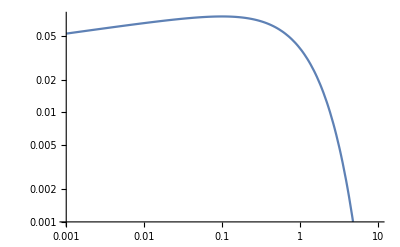

```mathematica
n=0.1;
Sqrt[n]
lower = 0;
upper = Infinity;
N[Integrate[(a)*p[a,n],{a,lower,upper}, Assumptions->{a>0,a∈Reals}]]
N[Integrate[(a^2-(n)^2)*p[a,n],{a,lower,upper}, Assumptions->{a>0,a∈Reals}]]
LogLogPlot[a*p[a,n],{a,1*^-3,10}]
```